```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/andrei/Work/physics/B-physics/BcBcNLO/calc/BcBc/PV/larin/gamma/renorm

```mathematica
PrependTo[$Path,"/home/andrei/Work/physics/B-physics/BcBcNLO/calc/pkg"];
```

```mathematica
<<X`
```

Package-X v1.0.4, by Hiren H. Patel

For more information, see the

```mathematica
NumericQ[r]=True;
```

```mathematica
PackageXSubs={LDot[p3,p3]->m^2,LDot[p4,p4]->m^2,LDot[p3,p4]->s/2-m^2,mc-> r m, mb-> (1-r) m};
```

```mathematica
toABC={pvA[a_,b_]:>A[b],pvB[a_,b_,c___]:>B[c],pvC[a_,b_,c_,d___]:>C[d],pvC0[a__]:>C[a]};
topvABC={A[a_]:>pvA[0,a],B[a__]:>pvB[0,0,a],C[a__]:>pvC[0,0,0,a]};
```

```mathematica
factor=(Exp[EulerGamma] 1/(4 Pi))^-eps
```

ⅇ^(ℽ (-eps)) (4 π)^eps

```mathematica
ff=Gamma[1-2 eps]/(Gamma[1-eps]^2 Gamma[1+eps](4 Pi)^eps I/(16 Pi^2))
```

-(ⅈ (4 π)^(2-eps) 1-2 eps)/((1-eps)^2 eps+1)

```mathematica
invff=1/ff
```

(ⅈ (4 π)^(eps-2) (1-eps)^2 eps+1)/(1-2 eps)

```mathematica
Normal[Series[FullSimplify[1/factor invff],{eps,0,1}]]
```

ⅈ/(16 π^2)

```mathematica
norm=Expand[Normal[Series[FullSimplify[1/factor invff],{eps,0,2}]]/(I/(16 Pi^2))]
```

1-(π^2 eps^2)/12

```mathematica
Fb=(((1-r)^2 m^2)/mmu)^-eps
```

((m^2 (1-r)^2)/mmu)^-eps

```mathematica
Fc=((r^2 m^2)/mmu)^-eps
```

((m^2 r^2)/mmu)^-eps

```mathematica
Fb=Plus@@ Factor[List@@ Normal[Series[Fb,{eps,0,1}]]/.{Log[(m^2 (1-r)^2)/mmu]->Log[m^2/mmu]+ 2 Log[1-r]}]
```

1-eps (log(m^2/mmu)+2 log(1-r))

```mathematica
Fc=Plus@@ Factor[List@@ Normal[Series[Fc,{eps,0,1}]]/.{Log[(m^2 r^2)/mmu]->Log[m^2/mmu]+ 2 Log[r]}]
```

1-eps (log(m^2/mmu)+2 log(r))

```mathematica
A0[m_]:=m^2+m^2/eps+eps*m^2+(eps*m^2*Pi^2)/6+m^2*Log[mmu/m^2]+eps*m^2*Log[mmu/m^2]+(eps*m^2*Log[mmu/m^2]^2)/2
```

```mathematica
F21[z_]:=(1-eps)/(2 (1-2 eps) z)(1+z-(1-z)^(1-2 eps)-2 (1-z)^(1-2 eps) eps (eps PolyLog[1,1,z]+Hui eps^2 Sum[(-2)^(j-k) PolyLog[k,3-k],{k,1,2}]))
```

```mathematica
B0polylog[s_,m1_,m2_]:=Block[{x,y,lam},If[m1≠ 0 && m2≠0,x=m1^2/s;y=m2^2/s;lam=√((1-x-y)^2-4 x y);  mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) (-s)^-eps ((Gamma[1-eps]^2 Gamma[eps])/Gamma[2-2 eps] lam^(1- 2 eps)-Gamma[-1+eps] 1/2(1+x-y-lam) (-x)^-eps F21[(1+x-y-lam)^2/(4 x)]-
Gamma[-1+eps] 1/2(1-x+y-lam) (-y)^-eps F21[(1-x+y-lam)^2/(4 y)]),If[m1==0 && m2 ≠ 0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) m2^(-2 eps) Gamma[1+eps]/(eps (1-eps))F21[s/m2^2],If[m1≠ 0 && m2== 0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) m1^(-2 eps) Gamma[1+eps]/(eps (1-eps))F21[s/m1^2],If[m1==0 && m2==0,mmu^eps(I Pi^(2-eps))/(2 Pi)^(4-2 eps) (-s)^-eps (Gamma[1-eps]^2 Gamma[eps])/Gamma[2-2 eps]]]]]]
```

```mathematica
<<cross-sectionNLOLarin.res
```

```mathematica
(* X[a_]:=norm *)
```

```mathematica
mc=1.5;mb=4.9;m=mc+mb;r=mc/m;CF=4/3;CA=3;pi=Pi;s=15^2;mt=175;R1=R2=1;nf=6;AL=1/137;
```

```mathematica
Sqrt[4 m^2]
```

12.8

```mathematica
(2mc+2 mc)^2
```

36.

```mathematica
pow[a_,b_]:=a^b
```

```mathematica
(* AS=0.3; mmu=(2 m)^2; *)
```

```mathematica
ex[1]=Collect[Expand[crosssection//N],{A[___],B[___],C[___]}]
```

-2.52175×10^-12 eps Aconj(1.5) AS^3-(1.821×10^-13 Aconj(1.5) AS^3)/eps+6.1664×10^-12 Aconj(1.5) AS^3-6.7123×10^-13 eps Aconj(4.9) AS^3+(5.57448×10^-14 Aconj(4.9) AS^3)/eps+3.72108×10^-12 Aconj(4.9) AS^3-7.89119×10^-14 eps Aconj(175.) AS^3+2.36736×10^-13 Aconj(175.) AS^3-7.0284×10^-11 eps Bconj(12.3596,0.,0.) AS^3+6.60071×10^-11 Bconj(12.3596,0.,0.) AS^3+1.60635×10^-13 eps Bconj(12.3596,1.5,1.5) AS^3+(1.62181×10^-12 Bconj(12.3596,1.5,1.5) AS^3)/eps-4.70577×10^-12 Bconj(12.3596,1.5,1.5) AS^3-4.28205×10^-12 eps Bconj(12.3596,4.9,4.9) AS^3-9.165×10^-12 Bconj(12.3596,4.9,4.9) AS^3-4.85899×10^-9 eps Bconj(12.3596,175.,175.) AS^3-7.2907×10^-9 Bconj(12.3596,175.,175.) AS^3+1.60514×10^-12 eps Bconj(51.9348,1.5,4.9) AS^3-(2.08617×10^-12 Bconj(51.9348,1.5,4.9) AS^3)/eps+5.44184×10^-12 Bconj(51.9348,1.5,4.9) AS^3-7.89403×10^-12 eps Bconj(51.9348,4.9,1.5) AS^3-(2.08617×10^-12 Bconj(51.9348,4.9,1.5) AS^3)/eps+3.10736×10^-12 Bconj(51.9348,4.9,1.5) AS^3+3.02202×10^-11 eps Bconj(76.7444,0.,4.9) AS^3+3.10062×10^-11 Bconj(76.7444,0.,4.9) AS^3+8.48727×10^-11 eps Bconj(76.7444,4.9,0.) AS^3-1.2889×10^-10 Bconj(76.7444,4.9,0.) AS^3-3.92014×10^-11 eps Bconj(131.891,0.,0.) AS^3+6.91296×10^-12 Bconj(131.891,0.,0.) AS^3-1.33978×10^-12 eps Bconj(131.891,1.5,1.5) AS^3+2.56767×10^-12 Bconj(131.891,1.5,1.5) AS^3+2.85383×10^-13 eps Bconj(131.891,4.9,4.9) AS^3+(1.62181×10^-12 Bconj(131.891,4.9,4.9) AS^3)/eps+7.47239×10^-13 Bconj(131.891,4.9,4.9) AS^3+2.60993×10^-11 eps Bconj(131.891,175.,175.) AS^3+3.92755×10^-11 Bconj(131.891,175.,175.) AS^3+8.48229×10^-11 eps Bconj(174.516,0.,1.5) AS^3-3.5298×10^-11 Bconj(174.516,0.,1.5) AS^3+1.39095×10^-11 eps Bconj(174.516,1.5,0.) AS^3-2.10477×10^-12 Bconj(174.516,1.5,0.) AS^3-5.76531×10^-11 eps Bconj(225.,1.5,1.5) AS^3+2.83803×10^-11 Bconj(225.,1.5,1.5) AS^3+2.50106×10^-11 eps Bconj(225.,4.9,4.9) AS^3-2.90097×10^-11 Bconj(225.,4.9,4.9) AS^3+8.56241×10^-11 eps Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3-1.94097×10^-11 Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3-4.78812×10^-10 eps Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3+3.9279×10^-10 Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3-2.3342×10^-11 eps Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3-1.54648×10^-11 Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3+2.92432×10^-10 eps Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3-4.2362×10^-11 Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3-3.40088×10^-11 eps Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3-5.75816×10^-11 Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3-1.07421×10^-9 eps Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3+4.31064×10^-10 Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3+8.47682×10^-10 eps Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3-1.06464×10^-9 Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3+1.06334×10^-10 eps Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3+1.13572×10^-10 Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3-5.74156×10^-10 eps Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3-9.36466×10^-10 Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3+9.13503×10^-10 eps Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3-9.20394×10^-10 Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3-1.3164×10^-9 eps Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3+1.03115×10^-9 Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3+6.8573×10^-11 eps Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3+7.38977×10^-12 Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3-3.88338×10^-12 eps Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3-5.83819×10^-12 Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3+5.898×10^-11 eps Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3-4.43848×10^-12 Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3+1.00945×10^-9 eps Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3-4.06886×10^-10 Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3-4.33068×10^-11 eps Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3+3.97861×10^-11 Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3+1.5365×10^-9 eps Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3+1.41484×10^-10 Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3+7.64523×10^-11 eps Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3-4.16826×10^-12 Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3+2.92629×10^-11 eps Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3+8.87697×10^-12 Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3+6.13595×10^-10 eps Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3-2.68271×10^-10 Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3+4.56976×10^-12 eps Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3-1.73772×10^-11 Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3+3.34604×10^-11 log(0.234375) AS^3+5.19077×10^-11 log(0.765625) AS^3-4.2684×10^-11 log(0.0244141 mmu) AS^3-(7.18005×10^-11 AS^3)/eps-6.02905×10^-11 AS^3+2.61349×10^-11 AS^2+(-2.52175×10^-12 eps AS^3-(1.821×10^-13 AS^3)/eps+6.1664×10^-12 AS^3) A(1.5)+(-6.7123×10^-13 eps AS^3+(5.57448×10^-14 AS^3)/eps+3.72108×10^-12 AS^3) A(4.9)+(2.36736×10^-13 AS^3-7.89119×10^-14 AS^3 eps) A(175.)+(6.60071×10^-11 AS^3-7.0284×10^-11 AS^3 eps) B(12.3596,0.,0.)+(1.60635×10^-13 eps AS^3+(1.62181×10^-12 AS^3)/eps-4.70577×10^-12 AS^3) B(12.3596,1.5,1.5)+(-4.28205×10^-12 eps AS^3-9.165×10^-12 AS^3) B(12.3596,4.9,4.9)+(-4.85899×10^-9 eps AS^3-7.2907×10^-9 AS^3) B(12.3596,175.,175.)+(1.60514×10^-12 eps AS^3-(2.08617×10^-12 AS^3)/eps+5.44184×10^-12 AS^3) B(51.9348,1.5,4.9)+(-7.89403×10^-12 eps AS^3-(2.08617×10^-12 AS^3)/eps+3.10736×10^-12 AS^3) B(51.9348,4.9,1.5)+(3.02202×10^-11 eps AS^3+3.10062×10^-11 AS^3) B(76.7444,0.,4.9)+(8.48727×10^-11 AS^3 eps-1.2889×10^-10 AS^3) B(76.7444,4.9,0.)+(6.91296×10^-12 AS^3-3.92014×10^-11 AS^3 eps) B(131.891,0.,0.)+(2.56767×10^-12 AS^3-1.33978×10^-12 AS^3 eps) B(131.891,1.5,1.5)+(2.85383×10^-13 eps AS^3+(1.62181×10^-12 AS^3)/eps+7.47239×10^-13 AS^3) B(131.891,4.9,4.9)+(2.60993×10^-11 eps AS^3+3.92755×10^-11 AS^3) B(131.891,175.,175.)+(8.48229×10^-11 AS^3 eps-3.5298×10^-11 AS^3) B(174.516,0.,1.5)+(1.39095×10^-11 AS^3 eps-2.10477×10^-12 AS^3) B(174.516,1.5,0.)+(2.83803×10^-11 AS^3-5.76531×10^-11 AS^3 eps) B(225.,1.5,1.5)+(2.50106×10^-11 AS^3 eps-2.90097×10^-11 AS^3) B(225.,4.9,4.9)+(8.56241×10^-11 AS^3 eps-1.94097×10^-11 AS^3) C[2.25,12.3596,2.25,0,1.5,0]+(3.9279×10^-10 AS^3-4.78812×10^-10 AS^3 eps) C[2.25,76.7444,40.96,4.9,1.5,0]+(-2.3342×10^-11 eps AS^3-1.54648×10^-11 AS^3) C[2.25,76.7444,51.9348,4.9,1.5,0]+(2.92432×10^-10 AS^3 eps-4.2362×10^-11 AS^3) C[2.25,131.891,174.516,0,1.5,0]+(-3.40088×10^-11 eps AS^3-5.75816×10^-11 AS^3) C[2.25,174.516,131.891,1.5,1.5,0]+(4.31064×10^-10 AS^3-1.07421×10^-9 AS^3 eps) C[2.25,174.516,225,1.5,1.5,0]+(8.47682×10^-10 AS^3 eps-1.06464×10^-9 AS^3) C[24.01,12.3596,76.7444,0,4.9,0]+(1.06334×10^-10 eps AS^3+1.13572×10^-10 AS^3) C[24.01,76.7444,12.3596,4.9,4.9,0]+(-5.74156×10^-10 eps AS^3-9.36466×10^-10 AS^3) C[24.01,76.7444,225,4.9,4.9,0]+(9.13503×10^-10 AS^3 eps-9.20394×10^-10 AS^3) C[24.01,131.891,24.01,0,4.9,0]+(1.03115×10^-9 AS^3-1.3164×10^-9 AS^3 eps) C[24.01,174.516,40.96,1.5,4.9,0]+(6.8573×10^-11 eps AS^3+7.38977×10^-12 AS^3) C[24.01,174.516,51.9348,1.5,4.9,0]+(-3.88338×10^-12 eps AS^3-5.83819×10^-12 AS^3) C[51.9348,51.9348,225,1.5,1.5,4.9]+(5.898×10^-11 AS^3 eps-4.43848×10^-12 AS^3) C[76.7444,2.25,51.9348,1.5,4.9,0]+(1.00945×10^-9 AS^3 eps-4.06886×10^-10 AS^3) C[76.7444,12.3596,24.01,0,4.9,0]+(3.97861×10^-11 AS^3-4.33068×10^-11 AS^3 eps) C[76.7444,24.01,12.3596,4.9,4.9,0]+(1.5365×10^-9 eps AS^3+1.41484×10^-10 AS^3) C[76.7444,24.01,225,4.9,4.9,0]+(7.64523×10^-11 AS^3 eps-4.16826×10^-12 AS^3) C[174.516,2.25,131.891,1.5,1.5,0]+(2.92629×10^-11 eps AS^3+8.87697×10^-12 AS^3) C[174.516,24.01,51.9348,4.9,1.5,0]+(6.13595×10^-10 AS^3 eps-2.68271×10^-10 AS^3) C[174.516,131.891,2.25,0,1.5,0]+(4.56976×10^-12 AS^3 eps-1.73772×10^-11 AS^3) C[225,51.9348,51.9348,1.5,4.9,4.9]

```mathematica
Bconj[s,0.,0.]/.{Bconj[s_,0.,0.]:> Expand[ExpandAll[Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]]]]/.{Conjugate[eps]-> eps,Conjugate[Log[mmu]]-> Log[mmu],Conjugate[eps Log[mmu]]-> eps Log[mmu]}]}
```

-(3.4161+3.14159 ⅈ) eps log(mmu)+(2.90007+10.732 ⅈ) eps-(3.4161+3.14159 ⅈ)+0.5 eps log^2(mmu)+1/eps+log(mmu)

```mathematica
ex[2]=Expand[Simplify[Normal[Series[ex[1]/.{A[m_]:> A0[m],B[s_,0.,0.]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]],B[s_,m_,0.]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]],B[s_,0.,m_]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]],B[s_,m1_,m2_]:> FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]],Aconj[m_]:> Conjugate[A0[m]],Bconj[s_,0.,0.]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,0] ,{eps,0,1}]]]],Bconj[s_,m_,0.]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m,0] ,{eps,0,1}]]]],Bconj[s_,0.,m_]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,0,m] ,{eps,0,1}]]]],Bconj[s_,m1_,m2_]:> Conjugate[FullSimplify[Normal[Series[ff B0polylog[s+0.00000001 I,m1,m2] ,{eps,0,1}]]]],log[a_]:>  Log[a]},{eps,0,0}]]/.{Log[a_ mmu]-> Log[a]+Log[mmu]}]/.{Conjugate[eps]-> eps,Conjugate[Log[mmu]]-> Log[mmu],Conjugate[eps Log[mmu]]-> eps Log[mmu]}]
```

(-3.76004×10^-7+4.45798×10^-10 ⅈ) eps^2 AS^3-(3.60556×10^-9-6.9051×10^-23 ⅈ) eps^2 log^2(mmu) AS^3+(3.6829×10^-11-3.01783×10^-27 ⅈ) eps log^2(mmu) AS^3+(1.67617×10^-26+6.10125×10^-33 ⅈ) log^2(mmu) AS^3+(9.44899×10^-9-2.58494×10^-25 ⅈ) eps AS^3+(8.56241×10^-11-2.52435×10^-29 ⅈ) eps C[2.25,12.3596,2.25,0,1.5,0] AS^3-(1.94097×10^-11-6.31089×10^-30 ⅈ) C[2.25,12.3596,2.25,0,1.5,0] AS^3-4.78812×10^-10 eps C[2.25,76.7444,40.96,4.9,1.5,0] AS^3+(3.9279×10^-10+3.50325×10^-46 ⅈ) C[2.25,76.7444,40.96,4.9,1.5,0] AS^3-(2.3342×10^-11-1.89327×10^-29 ⅈ) eps C[2.25,76.7444,51.9348,4.9,1.5,0] AS^3-(1.54648×10^-11+1.09476×10^-47 ⅈ) C[2.25,76.7444,51.9348,4.9,1.5,0] AS^3+(2.92432×10^-10+7.00649×10^-46 ⅈ) eps C[2.25,131.891,174.516,0,1.5,0] AS^3-4.2362×10^-11 C[2.25,131.891,174.516,0,1.5,0] AS^3-(3.40088×10^-11-6.31089×10^-30 ⅈ) eps C[2.25,174.516,131.891,1.5,1.5,0] AS^3-(5.75816×10^-11-3.78653×10^-29 ⅈ) C[2.25,174.516,131.891,1.5,1.5,0] AS^3-(1.07421×10^-9-1.00974×10^-27 ⅈ) eps C[2.25,174.516,225,1.5,1.5,0] AS^3+4.31064×10^-10 C[2.25,174.516,225,1.5,1.5,0] AS^3+(8.47682×10^-10+7.00649×10^-46 ⅈ) eps C[24.01,12.3596,76.7444,0,4.9,0] AS^3-(1.06464×10^-9-2.01948×10^-28 ⅈ) C[24.01,12.3596,76.7444,0,4.9,0] AS^3+(1.06334×10^-10+2.52435×10^-29 ⅈ) eps C[24.01,76.7444,12.3596,4.9,4.9,0] AS^3+(1.13572×10^-10-7.57306×10^-29 ⅈ) C[24.01,76.7444,12.3596,4.9,4.9,0] AS^3-5.74156×10^-10 eps C[24.01,76.7444,225,4.9,4.9,0] AS^3-(9.36466×10^-10-2.01948×10^-28 ⅈ) C[24.01,76.7444,225,4.9,4.9,0] AS^3+(9.13503×10^-10-2.01948×10^-28 ⅈ) eps C[24.01,131.891,24.01,0,4.9,0] AS^3-(9.20394×10^-10+2.01948×10^-28 ⅈ) C[24.01,131.891,24.01,0,4.9,0] AS^3-1.3164×10^-9 eps C[24.01,174.516,40.96,1.5,4.9,0] AS^3+(1.03115×10^-9-4.03897×10^-28 ⅈ) C[24.01,174.516,40.96,1.5,4.9,0] AS^3+(6.8573×10^-11-2.52435×10^-29 ⅈ) eps C[24.01,174.516,51.9348,1.5,4.9,0] AS^3+(7.38977×10^-12+1.09476×10^-47 ⅈ) C[24.01,174.516,51.9348,1.5,4.9,0] AS^3-(3.88338×10^-12-7.88861×10^-31 ⅈ) eps C[51.9348,51.9348,225,1.5,1.5,4.9] AS^3-(5.83819×10^-12+1.64215×10^-47 ⅈ) C[51.9348,51.9348,225,1.5,1.5,4.9] AS^3+(5.898×10^-11-1.26218×10^-29 ⅈ) eps C[76.7444,2.25,51.9348,1.5,4.9,0] AS^3-(4.43848×10^-12-1.57772×10^-30 ⅈ) C[76.7444,2.25,51.9348,1.5,4.9,0] AS^3+(1.00945×10^-9-4.03897×10^-28 ⅈ) eps C[76.7444,12.3596,24.01,0,4.9,0] AS^3-(4.06886×10^-10+1.00974×10^-28 ⅈ) C[76.7444,12.3596,24.01,0,4.9,0] AS^3-(4.33068×10^-11-2.52435×10^-29 ⅈ) eps C[76.7444,24.01,12.3596,4.9,4.9,0] AS^3+(3.97861×10^-11-1.26218×10^-29 ⅈ) C[76.7444,24.01,12.3596,4.9,4.9,0] AS^3+(1.5365×10^-9+8.07794×10^-28 ⅈ) eps C[76.7444,24.01,225,4.9,4.9,0] AS^3+(1.41484×10^-10-5.04871×10^-29 ⅈ) C[76.7444,24.01,225,4.9,4.9,0] AS^3+(7.64523×10^-11-7.57306×10^-29 ⅈ) eps C[174.516,2.25,131.891,1.5,1.5,0] AS^3-4.16826×10^-12 C[174.516,2.25,131.891,1.5,1.5,0] AS^3+2.92629×10^-11 eps C[174.516,24.01,51.9348,4.9,1.5,0] AS^3+(8.87697×10^-12+3.15544×10^-30 ⅈ) C[174.516,24.01,51.9348,4.9,1.5,0] AS^3+(6.13595×10^-10-2.01948×10^-28 ⅈ) eps C[174.516,131.891,2.25,0,1.5,0] AS^3-(2.68271×10^-10-5.04871×10^-29 ⅈ) C[174.516,131.891,2.25,0,1.5,0] AS^3+(4.56976×10^-12+3.15544×10^-30 ⅈ) eps C[225,51.9348,51.9348,1.5,4.9,4.9] AS^3-(1.73772×10^-11+1.26218×10^-29 ⅈ) C[225,51.9348,51.9348,1.5,4.9,4.9] AS^3+(8.56241×10^-11-2.52435×10^-29 ⅈ) eps Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3-(1.94097×10^-11-6.31089×10^-30 ⅈ) Cconj(2.25,12.3596,2.25,0.,1.5,0.) AS^3-4.78812×10^-10 eps Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3+(3.9279×10^-10+3.50325×10^-46 ⅈ) Cconj(2.25,76.7444,40.96,4.9,1.5,0.) AS^3-(2.3342×10^-11-1.89327×10^-29 ⅈ) eps Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3-(1.54648×10^-11+1.09476×10^-47 ⅈ) Cconj(2.25,76.7444,51.9348,4.9,1.5,0.) AS^3+(2.92432×10^-10+7.00649×10^-46 ⅈ) eps Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3-4.2362×10^-11 Cconj(2.25,131.891,174.516,0.,1.5,0.) AS^3-(3.40088×10^-11-6.31089×10^-30 ⅈ) eps Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3-(5.75816×10^-11-3.78653×10^-29 ⅈ) Cconj(2.25,174.516,131.891,1.5,1.5,0.) AS^3-(1.07421×10^-9-1.00974×10^-27 ⅈ) eps Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3+4.31064×10^-10 Cconj(2.25,174.516,225.,1.5,1.5,0.) AS^3+(8.47682×10^-10+7.00649×10^-46 ⅈ) eps Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3-(1.06464×10^-9-2.01948×10^-28 ⅈ) Cconj(24.01,12.3596,76.7444,0.,4.9,0.) AS^3+(1.06334×10^-10+2.52435×10^-29 ⅈ) eps Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3+(1.13572×10^-10-7.57306×10^-29 ⅈ) Cconj(24.01,76.7444,12.3596,4.9,4.9,0.) AS^3-5.74156×10^-10 eps Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3-(9.36466×10^-10-2.01948×10^-28 ⅈ) Cconj(24.01,76.7444,225.,4.9,4.9,0.) AS^3+(9.13503×10^-10-2.01948×10^-28 ⅈ) eps Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3-(9.20394×10^-10+2.01948×10^-28 ⅈ) Cconj(24.01,131.891,24.01,0.,4.9,0.) AS^3-1.3164×10^-9 eps Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3+(1.03115×10^-9-4.03897×10^-28 ⅈ) Cconj(24.01,174.516,40.96,1.5,4.9,0.) AS^3+(6.8573×10^-11-2.52435×10^-29 ⅈ) eps Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3+(7.38977×10^-12+1.09476×10^-47 ⅈ) Cconj(24.01,174.516,51.9348,1.5,4.9,0.) AS^3-(3.88338×10^-12-7.88861×10^-31 ⅈ) eps Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3-(5.83819×10^-12+1.64215×10^-47 ⅈ) Cconj(51.9348,51.9348,225.,1.5,1.5,4.9) AS^3+(5.898×10^-11-1.26218×10^-29 ⅈ) eps Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3-(4.43848×10^-12-1.57772×10^-30 ⅈ) Cconj(76.7444,2.25,51.9348,1.5,4.9,0.) AS^3+(1.00945×10^-9-4.03897×10^-28 ⅈ) eps Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3-(4.06886×10^-10+1.00974×10^-28 ⅈ) Cconj(76.7444,12.3596,24.01,0.,4.9,0.) AS^3-(4.33068×10^-11-2.52435×10^-29 ⅈ) eps Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3+(3.97861×10^-11-1.26218×10^-29 ⅈ) Cconj(76.7444,24.01,12.3596,4.9,4.9,0.) AS^3+(1.5365×10^-9+8.07794×10^-28 ⅈ) eps Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3+(1.41484×10^-10-5.04871×10^-29 ⅈ) Cconj(76.7444,24.01,225.,4.9,4.9,0.) AS^3+(7.64523×10^-11-7.57306×10^-29 ⅈ) eps Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3-4.16826×10^-12 Cconj(174.516,2.25,131.891,1.5,1.5,0.) AS^3+2.92629×10^-11 eps Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3+(8.87697×10^-12+3.15544×10^-30 ⅈ) Cconj(174.516,24.01,51.9348,4.9,1.5,0.) AS^3+(6.13595×10^-10-2.01948×10^-28 ⅈ) eps Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3-(2.68271×10^-10-5.04871×10^-29 ⅈ) Cconj(174.516,131.891,2.25,0.,1.5,0.) AS^3+(4.56976×10^-12+3.15544×10^-30 ⅈ) eps Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3-(1.73772×10^-11+1.26218×10^-29 ⅈ) Cconj(225.,51.9348,51.9348,1.5,4.9,4.9) AS^3+(7.22939×10^-8-8.1355×10^-11 ⅈ) eps^2 log(mmu) AS^3+(1.67594×10^-10+2.58494×10^-26 ⅈ) eps log(mmu) AS^3+((3.35234×10^-26-1.12104×10^-44 ⅈ) log(mmu) AS^3)/eps+(2.91165×10^-11+3.48553×10^-28 ⅈ) log(mmu) AS^3-((2.67139×10^-21+1.89327×10^-28 ⅈ) AS^3)/eps+((3.22444×10^-26+5.06379×10^-33 ⅈ) AS^3)/eps^2+(2.07712×10^-10+2.96864×10^-26 ⅈ) AS^3+(2.61349×10^-11+6.31089×10^-30 ⅈ) AS^2

```mathematica
ex[3]=Expand[Chop[LoopRefine[Expand[Normal[Series[ex[2],{eps,0,0}]]/.{Cconj[a___]:> Conjugate[C[a]]}]/.topvABC],10^(-20)]]
```

2.91165×10^-11 AS^3 log(mmu)-4.62859×10^-11 AS^3+2.61349×10^-11 AS^2

```mathematica
ex[4]=Collect[Chop[ex[3],10^(-20)],AS]/.{AS-> z *0.3}//Expand
```

7.86145×10^-13 z^3 log(mmu)-1.24972×10^-12 z^3+2.35214×10^-12 z^2

```mathematica
ratioCrossSection[mu2_]:=Abs[N[Coefficient[ex[4],z^3]/Coefficient[ex[4],z^2]/.{mmu-> mu2}]]
```

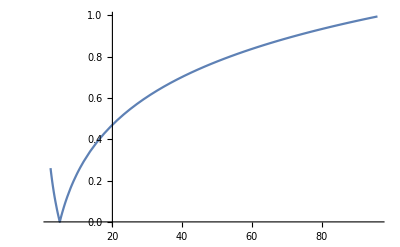

```mathematica
Plot[ratioCrossSection[mmu],{mmu,(mc)^2,(2mb)^2}]
```

```mathematica
ratioCrossSection[(2mc)^2]
```

0.203057

```mathematica
CrossSectionRatio=Abs[N[Coefficient[ex[4],z^3]/Coefficient[ex[4],z^2]]]/.{mmu-> m^2}
```

0.709533

```mathematica
Chop[Expand[ex[4]0.3894 10^12/.{mmu-> (2 mc)^2}],10^(-9)]
```

0.185985 z^3+0.915924 z^2